# The Journeyman Chess Engine

Jay Warendorff

May 27 2022 20:01

The Journeyman chess engine is written in the C language in a single .c file which may be compiled in Visual Studio to make a .exe file for Windows. It is a full-featured engine, but relatively simple employing no advanced algorithms. Rather than using a transposition table, it uses a history table. It is mostly based on the Video Instruction Chess Engine up through video #82 at this page:

https://www.chessprogramming.org/Vice

For simplicity, changes have been made to the code so that the board representation is an array of 64 integers instead of a 120 array of integers which seems a little more difficult to understand. This document is intended to explain how the Journeyman chess engine works.

Features include: Full support to play against from the Arena chess GUI and the capability to play against other chess engines in that GUI. Also implemented is the capability to set up a board position and play against the engine from that position. The engine implements the alpha-beta pruning algorithm together with move ordering to significantly increase the search depth over minimax for any fixed amount of time to search the chess tree for a given board position.

The rules of chess as well as the fundamentals of the C are assumed to be known by our readers.

## Overview

Coming

## History

Version 1.0 - 22 Feb 2022

## Strength

Version 1.0 seems to be close to 1700 elo in 2’+1” blitz using the Perfect 2010 (up to 12 half moves) opening book that comes with Arena.

## Obtaining the Source Code and Executable for Version 1.0

They may be downloaded here:

https://github.com/cH141PiEng/Journeyman-Chess-Engine/releases/tag/v1.0

## GUI to Run the Engine In

You may get the Windows version here

http://www.playwitharena.de/

## Board Representation

For the squares of the board a1 is represented by 0, b1 by 1,..., a8 by 56, ... h8 by 63. We also make use of no_sq = 64.

So we define the following enum:

enum {
    a1 = 0, b1, c1, d1, e1, f1, g1, h1,
    a2 = 8, b2, c2, d2, e2, f2, g2, h2,
    a3 = 16, b3, c3, d3, e3, f3, g3, h3,
    a4 = 24, b4, c4, d4, e4, f4, g4, h4,
    a5 = 32, b5, c5, d5, e5, f5, g5, h5,
    a6 = 40, b6, c6, d6, e6, f6, g6, h6,
    a7 = 48, b7, c7, d7, e7, f7, g7, h7,
    a8 = 56, b8, c8, d8, e8, f8, g8, h8, no_sq
};

We also use an enum to represent the pieces, with the empty piece being 0:

enum { e = 0, P, N, B, R, Q, K, p, n, b, r, q, k };

We use enums for the files, ranks and colors:

enum { FILE_A, FILE_B, FILE_C, FILE_D, FILE_E, FILE_F, FILE_G, FILE_H, FILE_NONE };
enum { RANK_1, RANK_2, RANK_3, RANK_4, RANK_5, RANK_6, RANK_7, RANK_8, RANK_NONE };

enum { WHITE, BLACK, BOTH };

We also define:

#define FALSE 0
#define TRUE  1

#define BRD_SQ_NUM 64

For pawns we will be using 64 bit integers to store the positions of the white pawns, the black pawns and both colors of pawns. So for convenience we define U64:

typedef unsigned long long U64;

This will make the evaluation of such things as passed and doubled pawns easier and more efficient.

We need to be able to set up a position on the board. First we need a board structure.

typedef struct {

    int pieces[BRD_SQ_NUM]; //Pieces corresponding to each squares
    U64 pawns[3]; //Pawn bitboards - white, black, both, a bit is set to a 1 if the corresponding color on that square has a pawn and 0 otherwise
                                  // 00000000 11111111 00000000 00000000 00000000 00000000 00000000 00000000 the white pawn bitboard for the standard startposition.

    int KingSq[2]; //King square for white and black

    int side;//Current side to move
    int enPas;//the enpassant square if there is one, otherwise set to no_sq
    int fiftyMove;//Uses half moves so when 100 game is drawn

    int ply;//How many half moves we are into the current search
    int hisPly;//How many half moves in total game so far - needed for looking back and determining repetitions

    int castlePerm;//stores castle permissions

    U64 posKey;//A unique key/number generated for each position (move)
    //representing the position on the board, used to detect using
    //the history array if we have repetitions in the position
    //posKey idea introduced in video 11

    int pceNum[13];//number of pieces on the board indexed by piece type
    int bigPce[2];//number of all pieces except pawns
    int majPce[2];//number of rooks and queens for white and black
    int minPce[2];//number of knights and bishops for white and black 
    int material[2];//material value for white and black

} S_BOARD;

For castling permissions we introduce the following for white kingside castling permissions, white queenside castling permissions, etc. The castling permissions will be represented by 4 bits. It is easier to store permissions in a single integer.

enum { WKCA = 1, WQCA = 2, BKCA = 4, BQCA = 8 };

binary    decimal

   0001       1  white king can castle to the king side
   0010       2  white king can castle to the queen side
   0100       4  black king can castle to the king side
   1000       8  black king can castle to the queen side

   examples:

   1111       both sides an castle both directions
   1001       black king => queen side
                    white king => king side

and we add this to the board structure

int castlePerm;

Next we will look at how we can store the history of the game to undo moves as needed and detect a threefold repetition.

Max # of half moves expected in a game:

#define MAXGAMEMOVES 2048

We need to define a structure that contains the information that will allow us to undo a move (will will be storing a move as an integer which will be covered later)

typedef struct {

    int move;
    int castlePerm; // before that move was played
    int enPas;
    int fiftyMove;
    U64 posKey;

} S_UNDO;

We need to create an array inside our board structure of undo information. Every time a move is made on the board, we will store in whatever move # we are at in the game, the move about to be made, and the values of the other items before making the move.

S_UNDO history[MAXGAMEMOVES];

For later use. Returns the square #, given the file and rank:

#define FR2SQ(f, r) ( (f) + ( (r) * 8 ) )

All the things we want to set up in the program before it starts running will be in the AllInit() function.

Suppose we want to generate all the moves for white - we can use a piece list. We add this to the board structure (13 - since there are 13 piece types and up to 10 of each):

int pList[13][10];

At first all the values are set to no_sq.

Example - add White knights at E1and D4 - pList[N][0] = E1; pList[N][1] = D4; We would loop through pList[N][i] until the value returned is no_sq. So we do not need to loop through all the squares on the board.

Makes the engine faster during move generation.

## Bitboard Utilities

Some functions for working with bitboards:

int Lsb(const U64 bb) {
    unsigned long index = -1;
    _BitScanForward64(&index, bb);
    return index;
}

// Returns the index of the least significant bit and unsets it
int PopBit(U64* bb) {

    int lsb = Lsb(*bb);
    *bb &= (*bb - 1);

    return lsb;
}

#define CountBits(bb) ((int) (__popcnt64(bb)))

We need a way to set and clear bits on a bitboard.

U64 SetMask[64];
U64 ClearMask[64];

void InitBitMasks() {
    int index = 0;

    for (index = 0; index < 64; index++) {
        SetMask[index] = 0ULL;
        ClearMask[index] = 0ULL;
    }

    for (index = 0; index < 64; index++) {
        SetMask[index] |= (1ULL << index);
        ClearMask[index] = ~SetMask[index];
    }
}

#define CLRBIT(bb,sq) ((bb) &= ClearMask[(sq)])
#define SETBIT(bb,sq) ((bb) |= SetMask[(sq)])

And we put InitBitMasks() into AllInit().

## Position Key

A unique key/number generated for each position (move) representing the position on the board, used to detect using the history array if we have repetitions in the position. Introduced in video 11. In the S_BOARD structure:

U64 posKey;

We need a way to generate a key for a chess board position.

U64 PieceKeys[13][64]; //Stores a random 64 bit number which states that that type of element is present on that sq number 
U64 SideKey; //Stores a random number if it is the turn of white in the game 
U64 CastleKeys[16]; //Stores 64 random numbers which represent each possible type of castle positions which are 0 to 15

Include stdlib.h to use rand() which generates a 15 bit random #
Fills 64 bits with random #s

#define RAND_64 	((U64)rand() | \
					(U64)rand() << 15 | \
					(U64)rand() << 30 | \
					(U64)rand() << 45 | \
					((U64)rand() & 0xf) << 60 )

This is a modified rand function which generates 64 bit random numbers for our poskey values.

Fills the variables with random numbers:

void InitHashKeys() {

    int index = 0;
    int index2 = 0;
    for (index = 0; index < 13; ++index) {
        for (index2 = 0; index2 < 64; ++index2) {
            PieceKeys[index][index2] = RAND_64;
        }
    }
    SideKey = RAND_64;
    for (index = 0; index < 16; ++index) {
        CastleKeys[index] = RAND_64;
    }
}

Put InitHashKeys() into the AllInit() function.

U64 GeneratePosKey(const S_BOARD* pos) {

    int sq = 0;
    U64 finalKey = 0;
    int piece = e;

    // pieces
    for (sq = 0; sq < BRD_SQ_NUM; ++sq) {
        piece = pos->pieces[sq];
        if (piece != no_sq && piece != e) {
            finalKey ^= PieceKeys[piece][sq];
        }
    }

    if (pos->side == WHITE) {
        finalKey ^= SideKey;
    }

    if (pos->enPas != no_sq) {
        finalKey ^= PieceKeys[e][pos->enPas];
    }

    finalKey ^= CastleKeys[pos->castlePerm];

    return finalKey;
}

## Setup a Position, FEN notation

Before defining the function for setting up a board, we first need one to reset the board - removes all the pieces from the board and all the values inside the S_Board structure to 0.

void ResetBoard(S_BOARD* pos) {

    int index = 0;

    for (index = 0; index < 64; ++index) {
        pos->pieces[index] = e;
    }

    for (index = 0; index < 2; ++index) {
        pos->bigPce[index] = 0;
        pos->majPce[index] = 0;
        pos->minPce[index] = 0;
        pos->material[index] = 0;
    }

    for (index = 0; index < 3; ++index) {
        pos->pawns[index] = 0ULL;
    }

    for (index = 0; index < 13; ++index) {
        pos->pceNum[index] = 0;
    }

    pos->KingSq[WHITE] = pos->KingSq[BLACK] = no_sq;

    pos->side = BOTH;
    pos->enPas = no_sq;
    pos->fiftyMove = 0;

    pos->ply = 0;
    pos->hisPly = 0;

    pos->castlePerm = 0;

    pos->posKey = 0ULL;

}

We will get into setting up a position on the board.

https://en.wikipedia.org/wiki/Forsyth%E2%80%93Edwards_Notation

#define START_FEN  “rnbqkbnr/pppppppp/8/8/8/8/PPPPPPPP/RNBQKBNR w KQkq - 0 1”

char PceChar[] = “.PNBRQKpnbrqk”;
char SideChar[] = “wb-“;
char RankChar[] = “12345678”;
char FileChar[] = “abcdefgh”;

#define IsBQ(p) (PieceBishopQueen[(p)])
#define IsRQ(p) (PieceRookQueen[(p)])
#define IsKn(p) (PieceKnight[(p)])
#define IsKi(p) (PieceKing[(p)])

This function takes in a FEN notation character array, and a pointer to S_BOARD structure

int ParseFen(char* fen, S_BOARD* pos) {

    int  rank = RANK_8;
    int  file = FILE_A;
    int  piece = 0;
    int  count = 0;
    int  i = 0;
    int  sq = 0;

    ResetBoard(pos);

    while ((rank >= RANK_1) && *fen) {
        count = 1;
        switch (*fen) {
        case ‘p’: piece = p; break;
        case ‘r’: piece = r; break;
        case ‘n’: piece = n; break;
        case ‘b’: piece = b; break;
        case ‘k’: piece = k; break;
        case ‘q’: piece = q; break;
        case ‘P’: piece = P; break;
        case ‘R’: piece = R; break;
        case ‘N’: piece = N; break;
        case ‘B’: piece = B; break;
        case ‘K’: piece = K; break;
        case ‘Q’: piece = Q; break;

        case ‘1’:
        case ‘2’:
        case ‘3’:
        case ‘4’:
        case ‘5’:
        case ‘6’:
        case ‘7’:
        case ‘8’:
            piece = e;
            count = *fen - ‘0’;
            break;

        case ‘/’:
        case ‘ ‘:
            rank--;
            file = FILE_A;
            fen++;
            continue;

        default:
            printf(“FEN error \n”);
            return -1;
        }

        for (i = 0; i < count; i++) {
            sq = rank * 8 + file;
            if (piece != e) {
                pos->pieces[sq] = piece;
            }
            file++;
        }
        fen++;
    }

    pos->side = (*fen == ‘w’) ? WHITE : BLACK;
    fen += 2;

    for (i = 0; i < 4; i++) {
        if (*fen == ‘ ‘) {
            break;
        }
        switch (*fen) {
        case ‘K’: pos->castlePerm |= WKCA; break;
        case ‘Q’: pos->castlePerm |= WQCA; break;
        case ‘k’: pos->castlePerm |= BKCA; break;
        case ‘q’: pos->castlePerm |= BQCA; break;
        default:	     break;
        }
        fen++;
    }
    fen++;

    if (*fen != ‘-‘) {
        file = fen[0] - ‘a’;
        rank = fen[1] - ‘1’;

        pos->enPas = FR2SQ(file, rank);
    }

    pos->posKey = GeneratePosKey(pos);

    UpdateListsMaterial(pos);

    return 0;
}

## Printing a Board to the Screen

Prints the board when it has been set up by in FEN notation

void PrintBoard(const S_BOARD* pos) {

    int sq, file, rank, piece;

    printf("\nGame Board:\n\n");

    for (rank = RANK_8; rank >= RANK_1; rank--) {
        printf("%d  ", rank + 1);
        for (file = FILE_A; file <= FILE_H; file++) {
            sq = FR2SQ(file, rank);
            piece = pos->pieces[sq];
            printf("%3c", PceChar[piece]);
        }
        printf("\n");
    }

    printf("\n   ");
    for (file = FILE_A; file <= FILE_H; file++) {
        printf("%3c", 'a' + file);
    }
    printf("\n");
    printf("side:%c\n", SideChar[pos->side]);
    printf("enPas:%d\n", pos->enPas);
    printf("castle:%c%c%c%c\n",
        pos->castlePerm & WKCA ? 'K' : '-',
        pos->castlePerm & WQCA ? 'Q' : '-',
        pos->castlePerm & BKCA ? 'k' : '-',
        pos->castlePerm & BQCA ? 'q' : '-'
    );
    printf("PosKey:%llX\n", pos->posKey);
}

## Piece Lists

int PieceBig[13] = { FALSE, FALSE, TRUE, TRUE, TRUE, TRUE, TRUE, FALSE, TRUE, TRUE, TRUE, TRUE, TRUE };
int PieceMaj[13] = { FALSE, FALSE, FALSE, FALSE, TRUE, TRUE, TRUE, FALSE, FALSE, FALSE, TRUE, TRUE, TRUE };
int PieceMin[13] = { FALSE, FALSE, TRUE, TRUE, FALSE, FALSE, FALSE, FALSE, TRUE, TRUE, FALSE, FALSE, FALSE };
int PieceVal[13] = { 0, 100, 325, 325, 550, 1000, 50000, 100, 325, 325, 550, 1000, 50000 };
int PieceCol[13] = { BOTH, WHITE, WHITE, WHITE, WHITE, WHITE, WHITE,
    BLACK, BLACK, BLACK, BLACK, BLACK, BLACK };

void UpdateListsMaterial(S_BOARD* pos) {

    int piece, sq, index, colour;

    for (index = 0; index < BRD_SQ_NUM; ++index) {
        sq = index;
        piece = pos->pieces[index];
        if (piece != e) {
            colour = PieceCol[piece];

            if (PieceBig[piece] == TRUE) pos->bigPce[colour]++;
            if (PieceMin[piece] == TRUE) pos->minPce[colour]++;
            if (PieceMaj[piece] == TRUE) pos->majPce[colour]++;

            pos->material[colour] += PieceVal[piece];

            pos->pList[piece][pos->pceNum[piece]] = sq;
            pos->pceNum[piece]++;

            if (piece == K) pos->KingSq[WHITE] = sq;
            if (piece == k) pos->KingSq[BLACK] = sq;

            if (piece == P) {
                SETBIT(pos->pawns[WHITE], sq);
                SETBIT(pos->pawns[BOTH], sq);
            }
            else if (piece == p) {
                SETBIT(pos->pawns[BLACK], sq);
                SETBIT(pos->pawns[BOTH], sq);
            }
        }
    }
}

## Rank and File Arrays

What file/rank is a square ? (add InitFilesRanksBrd() to AllInit()):

int FilesBrd[BRD_SQ_NUM];
int RanksBrd[BRD_SQ_NUM];

void InitFilesRanksBrd() {

    int index = 0;
    int file = FILE_A;
    int rank = RANK_1;
    int sq = a1;

    for (rank = RANK_1; rank <= RANK_8; ++rank) {
        for (file = FILE_A; file <= FILE_H; ++file) {
            sq = FR2SQ(file, rank);
            FilesBrd[sq] = file;
            RanksBrd[sq] = rank;
        }
    }
}

## SqAttacked

const int KnDir[8] = { -6, -17, -15, -10, 6, 17, 15, 10 };
const int RkDir[4] = { -1, -8, 1, 8 };
const int BiDir[4] = { -7, -9, 7, 9 };
const int KiDir[8] = { -1, -8, 1, 8, -7, -9, 7, 9 };

int PiecePawn[13] = { FALSE, TRUE, FALSE, FALSE, FALSE, FALSE, FALSE, TRUE, FALSE, FALSE, FALSE, FALSE, FALSE };
int PieceKnight[13] = { FALSE, FALSE, TRUE, FALSE, FALSE, FALSE, FALSE, FALSE, TRUE, FALSE, FALSE, FALSE, FALSE };
int PieceKing[13] = { FALSE, FALSE, FALSE, FALSE, FALSE, FALSE, TRUE, FALSE, FALSE, FALSE, FALSE, FALSE, TRUE };
int PieceRookQueen[13] = { FALSE, FALSE, FALSE, FALSE, TRUE, TRUE, FALSE, FALSE, FALSE, FALSE, TRUE, TRUE, FALSE };
int PieceBishopQueen[13] = { FALSE, FALSE, FALSE, TRUE, FALSE, TRUE, FALSE, FALSE, FALSE, TRUE, FALSE, TRUE, FALSE };
int PieceSlides[13] = { FALSE, FALSE, FALSE, TRUE, TRUE, TRUE, FALSE, FALSE, FALSE, TRUE, TRUE, TRUE, FALSE };

Is square attacked by side? - needed in particular to check if king is in check or squares in between king and rook to castle with are attacked by any piece of opposite color.

int SqAttacked(const int sq, const int side, const S_BOARD* pos) {

    int cs, rs, ct, rt, pce, index, t_sq, dir;

    cs = COL(sq);
    rs = ROW(sq);

    // pawns
    if (side == WHITE) {
        t_sq = sq - 9;
        ct = COL(t_sq);
        if (pos->pieces[sq - 9] == P && (0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
            return TRUE;
        }
        t_sq = sq - 7;
        ct = COL(t_sq);
        if (pos->pieces[t_sq] == P && (0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
            return TRUE;
        }
    }
    else {
        t_sq = sq + 9;
        ct = COL(t_sq);
        if (pos->pieces[t_sq] == p && (0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
            return TRUE;
        }
        t_sq = sq + 7;
        ct = COL(t_sq);
        if (pos->pieces[t_sq] == p && (0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
            return TRUE;
        }
    }

    // knights
    for (index = 0; index < 8; ++index) {
        t_sq = sq + KnDir[index];
        pce = pos->pieces[t_sq];
        ct = COL(t_sq);
        rt = ROW(t_sq);
        if (((0 <= t_sq) && (t_sq <= 63) && (-2 <= (cs - ct)) && ((cs - ct) <= 2) && (-2 <= (rs - rt)) && ((rs - rt) <= 2)) && IsKn(pce) && PieceCol[pce] == side) {
            return TRUE;
        }
    }

    // rooks, queens
    for (index = 0; index < 4; ++index) {
        dir = RkDir[index];
        t_sq = sq + dir;
        cs = COL(sq);
        rs = ROW(sq);
        ct = COL(t_sq);
        rt = ROW(t_sq);

        if ((0 <= t_sq) && (t_sq <= 63))
        {
            pce = pos->pieces[t_sq];
        }
        else
        {
            pce = e;
        }
        while ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1)) {
            if (pce != e) {
                if (IsRQ(pce) && PieceCol[pce] == side) {
                    return TRUE;
                }
                break;
            }
            cs = COL(t_sq);
            rs = ROW(t_sq);
            t_sq += dir;
            if ((0 <= t_sq) && (t_sq <= 63))
            {
                pce = pos->pieces[t_sq];
            }
            else
            {
                pce = e;
            }
            ct = COL(t_sq);
            rt = ROW(t_sq);
        }
    }

    // bishops, queens
    for (index = 0; index < 4; ++index) {
        dir = BiDir[index];
        t_sq = sq + dir;
        cs = COL(sq);
        rs = ROW(sq);
        ct = COL(t_sq);
        rt = ROW(t_sq);

        if ((0 <= t_sq) && (t_sq <= 63))
        {
            pce = pos->pieces[t_sq];
        }
        else
        {
            pce = e;
        }
        while ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1)) {
            if (pce != e) {
                if (IsBQ(pce) && PieceCol[pce] == side) {
                    return TRUE;
                }
                break;
            }
            cs = COL(t_sq);
            rs = ROW(t_sq);
            t_sq += dir; //if (sq == 4 && dir == 7) { printf("t_sq %d\n", t_sq); }
            if ((0 <= t_sq) && (t_sq <= 63))
            {
                pce = pos->pieces[t_sq];
            }
            else
            {
                pce = e;
            }
            ct = COL(t_sq);
            rt = ROW(t_sq);
        }
    }

    cs = COL(sq);
    rs = ROW(sq);

    // kings
    for (index = 0; index < 8; ++index) {
        t_sq = sq + KiDir[index];
        pce = pos->pieces[t_sq];
        ct = COL(t_sq);
        rt = ROW(t_sq);
        if (((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1)) && IsKi(pce) && PieceCol[pce] == side) {
            return TRUE;
        }
    }

    return FALSE;

}

## Move Structure

typedef struct {
    int move;
    int score;
} S_MOVE;

0000 0000 0000 0000 0000 0111 1111 -> From 0x7F
0000 0000 0000 0011 1111 1000 0000 -> To >> 7, 0x7F
0000 0000 0011 1100 0000 0000 0000 -> Captured >> 14, 0xF
0000 0000 0100 0000 0000 0000 0000 -> EP 0x40000
0000 0000 1000 0000 0000 0000 0000 -> Pawn Start 0x80000
0000 1111 0000 0000 0000 0000 0000 -> Promoted Piece >> 20, 0xF
0001 0000 0000 0000 0000 0000 0000 -> Castle 0x1000000

To find the masked value which will give the index of the move, captured type index and promoted type index

#define FROMSQ(m) ((m) & 0x7F)
#define TOSQ(m) (((m)>>7) & 0x7F)
#define CAPTURED(m) (((m)>>14) & 0xF)
#define PROMOTED(m) (((m)>>20) & 0xF)

The values which will &'d with moves to see if the corrsponding bits are set or not uses hexadecimal numbers

#define MFLAGEP 0x40000
#define MFLAGPS 0x80000
#define MFLAGCA 0x1000000

Flag to see if the capturing is happening or not

#define MFLAGCAP 0x7C000
#define MFLAGPROM 0xF00000

## PrintMove and PrintSquare

Print the file and rank of a current square using the file and rank arrays

char* PrSq(const int sq) {

    static char SqStr[3];

    int file = FilesBrd[sq];
    int rank = RanksBrd[sq];

    sprintf(SqStr, "%c%c", ('a' + file), ('1' + rank));

    return SqStr;

}

Print the from, to and promoted bit values of the move

char* PrMove(const int move) {

    static char MvStr[6];

    int ff = FilesBrd[FROMSQ(move)];
    int rf = RanksBrd[FROMSQ(move)];
    int ft = FilesBrd[TOSQ(move)];
    int rt = RanksBrd[TOSQ(move)];

    int promoted = PROMOTED(move);

    if (promoted) {
        char pchar = 'q';
        if (IsKn(promoted)) {
            pchar = 'n';
        }
        else if (IsRQ(promoted) && !IsBQ(promoted)) {
            pchar = 'r';
        }
        else if (!IsRQ(promoted) && IsBQ(promoted)) {
            pchar = 'b';
        }
        sprintf(MvStr, "%c%c%c%c%c", ('a' + ff), ('1' + rf), ('a' + ft), ('1' + rt), pchar);
    }
    else {
        sprintf(MvStr, "%c%c%c%c", ('a' + ff), ('1' + rf), ('a' + ft), ('1' + rt));
    }

    return MvStr;
}

## Move Generation

#define MOVE(f,t,ca,pro,fl) ( (f) | ((t) << 7) | ( (ca) << 14 ) | ( (pro) << 20 ) | (fl))

//These arrays enable generation of moves for sliding pieces of both sides as they define the starting 
//index of white and black sliding pieces and when we reach a 0 we have completed one side’s sliding pieces 
const int LoopSlidePce[8] = {
 B, R, Q, 0, b, r, q, 0
};

const int LoopNonSlidePce[6] = {
 N, K, 0, n, k, 0
};

const int LoopSlideIndex[2] = { 0, 4 };
const int LoopNonSlideIndex[2] = { 0, 3 };

//These store the directions for each piece which need to be added to the current square...to get all the squares 
//where a type of piece indexed by rows can move; 

const int PceDir[13][8] = {
    { 0, 0, 0, 0, 0, 0, 0 },
    { 0, 0, 0, 0, 0, 0, 0 },
    { -6, -17, -15, -10, 6, 17, 15, 10 },
    { -7, -9, 7, 9, 0, 0, 0, 0 },
    { -1, -8, 1, 8, 0, 0, 0, 0 },
    { -1, -8, 1, 8, -7, -9, 7, 9 },
    { -1, -8, 1, 8, -7, -9, 7, 9 },
    { 0, 0, 0, 0, 0, 0, 0 },
    { -6, -17, -15, -10, 6, 17, 15, 10 },
    { -7, -9, 7, 9, 0, 0, 0, 0 },
    { -1, -8, 1, 8, 0, 0, 0, 0 },
    { -1, -8, 1, 8, -7, -9, 7, 9 },
    { -1, -8, 1, 8, -7, -9, 7, 9 }
};

//The number of directions for each piece type - for queen 8, bishop and rook 4 
const int NumDir[13] = {
 0, 0, 8, 4, 4, 8, 8, 0, 8, 4, 4, 8, 8
};

void GenerateAllMoves(const S_BOARD* pos, S_MOVELIST* list);

static void AddQuietMove(const S_BOARD* pos, int move, S_MOVELIST* list) {

    list->moves[list->count].move = move;

    if (pos->searchKillers[0][pos->ply] == move) {
        list->moves[list->count].score = 900000;
    }
    else if (pos->searchKillers[1][pos->ply] == move) {
        list->moves[list->count].score = 800000;
    }
    else {
        list->moves[list->count].score = pos->searchHistory[pos->pieces[FROMSQ(move)]][TOSQ(move)];
    }
    list->count++;
}

static void AddCaptureMove(const S_BOARD* pos, int move, S_MOVELIST* list) {

    list->moves[list->count].move = move;
    list->moves[list->count].score = MvvLvaScores[CAPTURED(move)][pos->pieces[FROMSQ(move)]] + 1000000;
    list->count++;
}

static void AddEnPassantMove(const S_BOARD* pos, int move, S_MOVELIST* list) {

    list->moves[list->count].move = move;
    list->moves[list->count].score = 105 + 1000000;
    list->count++;
}

static void AddWhitePawnCapMove(const S_BOARD* pos, const int from, const int to, const int cap, S_MOVELIST* list) {

    if (RanksBrd[from] == RANK_7) {
        AddCaptureMove(pos, MOVE(from, to, cap, Q, 0), list);
        AddCaptureMove(pos, MOVE(from, to, cap, R, 0), list);
        AddCaptureMove(pos, MOVE(from, to, cap, B, 0), list);
        AddCaptureMove(pos, MOVE(from, to, cap, N, 0), list);
    }
    else {
        AddCaptureMove(pos, MOVE(from, to, cap, e, 0), list);
    }
}

static void AddWhitePawnMove(const S_BOARD* pos, const int from, const int to, S_MOVELIST* list) {

    if (RanksBrd[from] == RANK_7) {
        AddQuietMove(pos, MOVE(from, to, e, Q, 0), list);
        AddQuietMove(pos, MOVE(from, to, e, R, 0), list);
        AddQuietMove(pos, MOVE(from, to, e, B, 0), list);
        AddQuietMove(pos, MOVE(from, to, e, N, 0), list);
    }
    else {
        AddQuietMove(pos, MOVE(from, to, e, e, 0), list);
    }
}

static void AddBlackPawnCapMove(const S_BOARD* pos, const int from, const int to, const int cap, S_MOVELIST* list) {

    if (RanksBrd[from] == RANK_2) {
        AddCaptureMove(pos, MOVE(from, to, cap, q, 0), list);
        AddCaptureMove(pos, MOVE(from, to, cap, r, 0), list);
        AddCaptureMove(pos, MOVE(from, to, cap, b, 0), list);
        AddCaptureMove(pos, MOVE(from, to, cap, n, 0), list);
    }
    else {
        AddCaptureMove(pos, MOVE(from, to, cap, e, 0), list);
    }
}

static void AddBlackPawnMove(const S_BOARD* pos, const int from, const int to, S_MOVELIST* list) {

    if (RanksBrd[from] == RANK_2) {
        AddQuietMove(pos, MOVE(from, to, e, q, 0), list);
        AddQuietMove(pos, MOVE(from, to, e, r, 0), list);
        AddQuietMove(pos, MOVE(from, to, e, b, 0), list);
        AddQuietMove(pos, MOVE(from, to, e, n, 0), list);
    }
    else {
        AddQuietMove(pos, MOVE(from, to, e, e, 0), list);
    }
}

void GenerateAllMoves(const S_BOARD* pos, S_MOVELIST* list) {

    list->count = 0;

    int pce = e;
    int side = pos->side;
    int sq = 0; int t_sq = 0;
    int pceNum = 0;
    int dir = 0;
    int index = 0;
    int pceIndex = 0;

    int cs, ct, rs, rt;

    if (side == WHITE) {

        for (pceNum = 0; pceNum < pos->pceNum[P]; ++pceNum) {
            sq = pos->pList[P][pceNum];

            if ((sq + 8 <= 63) && pos->pieces[sq + 8] == e) {
                AddWhitePawnMove(pos, sq, sq + 8, list);
                if (RanksBrd[sq] == RANK_2 && pos->pieces[sq + 16] == e) {
                    AddQuietMove(pos, MOVE(sq, (sq + 16), e, e, MFLAGPS), list);
                }
            }

            t_sq = sq + 7;
            cs = COL(sq);
            ct = COL(t_sq);
            rs = ROW(sq);
            rt = ROW(t_sq);
            if ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1) && (PieceCol[pos->pieces[sq + 7]] == BLACK)) {
                AddWhitePawnCapMove(pos, sq, sq + 7, pos->pieces[sq + 7], list);
            }
            t_sq = sq + 9;
            ct = COL(t_sq);
            rt = ROW(t_sq);
            if ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1) && (PieceCol[pos->pieces[sq + 9]] == BLACK)) {
                AddWhitePawnCapMove(pos, sq, sq + 9, pos->pieces[sq + 9], list);
            }

            if (pos->enPas != no_sq) {
                ct = COL(sq + 7);
                if ((sq + 7 == pos->enPas) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
                    AddEnPassantMove(pos, MOVE(sq, sq + 7, e, e, MFLAGEP), list);
                }
                ct = COL(sq + 9);
                if ((sq + 9 == pos->enPas) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
                    AddEnPassantMove(pos, MOVE(sq, sq + 9, e, e, MFLAGEP), list);
                }
            }
        }

        if (pos->castlePerm & WKCA) {
            if (pos->pieces[f1] == e && pos->pieces[g1] == e) {
                if (!SqAttacked(e1, BLACK, pos) && !SqAttacked(f1, BLACK, pos)) {
                    AddQuietMove(pos, MOVE(e1, g1, e, e, MFLAGCA), list);
                }
            }
        }

        if (pos->castlePerm & WQCA) {
            if (pos->pieces[d1] == e && pos->pieces[c1] == e && pos->pieces[b1] == e) {
                if (!SqAttacked(e1, BLACK, pos) && !SqAttacked(d1, BLACK, pos)) {
                    AddQuietMove(pos, MOVE(e1, c1, e, e, MFLAGCA), list);
                }
            }
        }

    }
    else {

        for (pceNum = 0; pceNum < pos->pceNum[p]; ++pceNum) {
            sq = pos->pList[p][pceNum];

            if ((0 <= sq - 8) && pos->pieces[sq - 8] == e) {
                AddBlackPawnMove(pos, sq, sq - 8, list);
                if (RanksBrd[sq] == RANK_7 && pos->pieces[sq - 16] == e) {
                    AddQuietMove(pos, MOVE(sq, (sq - 16), e, e, MFLAGPS), list);
                }
            }

            t_sq = sq - 7;
            cs = COL(sq);
            ct = COL(t_sq);
            rs = ROW(sq);
            rt = ROW(t_sq);
            if ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1) && (PieceCol[pos->pieces[sq - 7]] == WHITE)) {
                AddBlackPawnCapMove(pos, sq, sq - 7, pos->pieces[sq - 7], list);
            }
            t_sq = sq - 9;
            ct = COL(t_sq);
            rt = ROW(t_sq);
            if ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1) && (PieceCol[pos->pieces[sq - 9]] == WHITE)) {
                AddBlackPawnCapMove(pos, sq, sq - 9, pos->pieces[sq - 9], list);
            }
            if (pos->enPas != no_sq) {
                ct = COL(sq - 7);
                if ((sq - 7 == pos->enPas) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
                    AddEnPassantMove(pos, MOVE(sq, sq - 7, e, e, MFLAGEP), list);
                }
                ct = COL(sq - 9);
                if ((sq - 9 == pos->enPas) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
                    AddEnPassantMove(pos, MOVE(sq, sq - 9, e, e, MFLAGEP), list);
                }
            }
        }

        // castling
        if (pos->castlePerm & BKCA) {
            if (pos->pieces[f8] == e && pos->pieces[g8] == e) {
                if (!SqAttacked(e8, WHITE, pos) && !SqAttacked(f8, WHITE, pos)) {
                    AddQuietMove(pos, MOVE(e8, g8, e, e, MFLAGCA), list);
                }
            }
        }

        if (pos->castlePerm & BQCA) {
            if (pos->pieces[d8] == e && pos->pieces[c8] == e && pos->pieces[b8] == e) {
                if (!SqAttacked(e8, WHITE, pos) && !SqAttacked(d8, WHITE, pos)) {
                    AddQuietMove(pos, MOVE(e8, c8, e, e, MFLAGCA), list);
                }
            }
        }
    }

    //The break statement ends the loop immediately when it is encountered. 
    //The continue statement skips the current iteration of the loop and continues with the next iteration. 

    /* Loop for slider pieces */
    pceIndex = LoopSlideIndex[side];
    pce = LoopSlidePce[pceIndex++];
    while (pce != 0) {		

        for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
            sq = pos->pList[pce][pceNum];

            for (index = 0; index < NumDir[pce]; ++index) {
                dir = PceDir[pce][index];
                t_sq = sq + dir;

                cs = COL(sq);
                ct = COL(t_sq);
                rs = ROW(sq);
                rt = ROW(t_sq);

                while ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1)) {
                    // BLACK ^ 1 == WHITE       WHITE ^ 1 == BLACK
                    if (pos->pieces[t_sq] != e) {
                        if (PieceCol[pos->pieces[t_sq]] == (side ^ 1)) {
                            AddCaptureMove(pos, MOVE(sq, t_sq, pos->pieces[t_sq], e, 0), list);
                        }
                        break;
                    }
                    AddQuietMove(pos, MOVE(sq, t_sq, e, e, 0), list);
                    cs = COL(t_sq);
                    rs = ROW(t_sq);
                    t_sq += dir;
                    ct = COL(t_sq);
                    rt = ROW(t_sq);
                }
            }
        }

        pce = LoopSlidePce[pceIndex++];
    }

    /* Loop for non slider */
    pceIndex = LoopNonSlideIndex[side];
    pce = LoopNonSlidePce[pceIndex++];

    while (pce != 0) {

        for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
            sq = pos->pList[pce][pceNum];

            for (index = 0; index < NumDir[pce]; ++index) {
                dir = PceDir[pce][index];
                t_sq = sq + dir;

                cs = COL(sq);
                ct = COL(t_sq);
                rs = ROW(sq);
                rt = ROW(t_sq);

                if ((pce == N || pce == n) && !((0 <= t_sq) && (t_sq <= 63) && (-2 <= (cs - ct)) && ((cs - ct) <= 2) && (-2 <= (rs - rt)) && ((rs - rt) <= 2)))
                {
                    continue;
                }

                if ((pce == K || pce == k) && !((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1)))
                {
                    continue;
                }

                // BLACK ^ 1 == WHITE       WHITE ^ 1 == BLACK
                if (pos->pieces[t_sq] != e) {
                    if (PieceCol[pos->pieces[t_sq]] == (side ^ 1)) {
                        AddCaptureMove(pos, MOVE(sq, t_sq, pos->pieces[t_sq], e, 0), list);
                    }
                    continue;
                }
                AddQuietMove(pos, MOVE(sq, t_sq, e, e, 0), list);
            }
        }

        pce = LoopNonSlidePce[pceIndex++];
    }
}

GenerateAllCaps is mostly the same function as GenerateAllMoves, but it only generates the capture moves which are required in the Quiescence search function

void GenerateAllCaps(const S_BOARD* pos, S_MOVELIST* list) {

    list->count = 0;

    int pce = e;
    int side = pos->side;
    int sq = 0; int t_sq = 0;
    int pceNum = 0;
    int dir = 0;
    int index = 0;
    int pceIndex = 0;

    int cs, ct, rs, rt;

    if (side == WHITE) {

        for (pceNum = 0; pceNum < pos->pceNum[P]; ++pceNum) {
            sq = pos->pList[P][pceNum];

            t_sq = sq + 7;
            cs = COL(sq);
            ct = COL(t_sq);
            rs = ROW(sq);
            rt = ROW(t_sq);
            if ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1) && (PieceCol[pos->pieces[sq + 7]] == BLACK)) {
                AddWhitePawnCapMove(pos, sq, sq + 7, pos->pieces[sq + 7], list);
            }
            t_sq = sq + 9;
            ct = COL(t_sq);
            rt = ROW(t_sq);
            if ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1) && PieceCol[pos->pieces[sq + 9]] == BLACK) {
                AddWhitePawnCapMove(pos, sq, sq + 9, pos->pieces[sq + 9], list);
            }

            if (pos->enPas != no_sq) {
                ct = COL(sq + 7);
                if ((sq + 7 == pos->enPas) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
                    AddEnPassantMove(pos, MOVE(sq, sq + 7, e, e, MFLAGEP), list);
                }
                ct = COL(sq + 9);
                if ((sq + 9 == pos->enPas) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
                    AddEnPassantMove(pos, MOVE(sq, sq + 9, e, e, MFLAGEP), list);
                }
            }
        }

    }
    else {

        for (pceNum = 0; pceNum < pos->pceNum[p]; ++pceNum) {
            sq = pos->pList[p][pceNum];

            t_sq = sq - 7;
            cs = COL(sq);
            ct = COL(t_sq);
            rs = ROW(sq);
            rt = ROW(t_sq);
            if ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1) && (PieceCol[pos->pieces[sq - 7]] == WHITE)) {
                AddBlackPawnCapMove(pos, sq, sq - 7, pos->pieces[sq - 7], list);
            }
            t_sq = sq - 9;
            ct = COL(t_sq);
            rt = ROW(t_sq);
            if ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1) && (PieceCol[pos->pieces[sq - 9]] == WHITE)) {
                AddBlackPawnCapMove(pos, sq, sq - 9, pos->pieces[sq - 9], list);
            }
            if (pos->enPas != no_sq) {
                ct = COL(sq - 7);
                if ((sq - 7 == pos->enPas) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
                    AddEnPassantMove(pos, MOVE(sq, sq - 7, e, e, MFLAGEP), list);
                }
                ct = COL(sq - 9);
                if ((sq - 9 == pos->enPas) && (-1 <= (cs - ct)) && ((cs - ct) <= 1)) {
                    AddEnPassantMove(pos, MOVE(sq, sq - 9, e, e, MFLAGEP), list);
                }
            }
        }
    }

    /* Loop for slider pieces */
    pceIndex = LoopSlideIndex[side];
    pce = LoopSlidePce[pceIndex++];
    while (pce != 0) {

        for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
            sq = pos->pList[pce][pceNum];

            for (index = 0; index < NumDir[pce]; ++index) {
                dir = PceDir[pce][index];
                t_sq = sq + dir;

                cs = COL(sq);
                ct = COL(t_sq);
                rs = ROW(sq);
                rt = ROW(t_sq);

                while ((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1)) {
                    // BLACK ^ 1 == WHITE       WHITE ^ 1 == BLACK
                    if (pos->pieces[t_sq] != e) {
                        if (PieceCol[pos->pieces[t_sq]] == (side ^ 1)) {
                            AddCaptureMove(pos, MOVE(sq, t_sq, pos->pieces[t_sq], e, 0), list);
                        }
                        break;
                    }
                    cs = COL(t_sq);
                    rs = ROW(t_sq);
                    t_sq += dir;
                    ct = COL(t_sq);
                    rt = ROW(t_sq);
                }
            }
        }

        pce = LoopSlidePce[pceIndex++];
    }

    /* Loop for non slider */
    pceIndex = LoopNonSlideIndex[side];
    pce = LoopNonSlidePce[pceIndex++];

    while (pce != 0) {

        for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
            sq = pos->pList[pce][pceNum];

            for (index = 0; index < NumDir[pce]; ++index) {
                dir = PceDir[pce][index];
                t_sq = sq + dir;

                cs = COL(sq);
                ct = COL(t_sq);
                rs = ROW(sq);
                rt = ROW(t_sq);

                if ((pce == N || pce == n) && !((0 <= t_sq) && (t_sq <= 63) && (-2 <= (cs - ct)) && ((cs - ct) <= 2) && (-2 <= (rs - rt)) && ((rs - rt) <= 2)))
                {
                    continue;
                }

                if ((pce == K || pce == k) && !((0 <= t_sq) && (t_sq <= 63) && (-1 <= (cs - ct)) && ((cs - ct) <= 1) && (-1 <= (rs - rt)) && ((rs - rt) <= 1)))
                {
                    continue;
                }

                // BLACK ^ 1 == WHITE       WHITE ^ 1 == BLACK
                if (pos->pieces[t_sq] != e) {
                    if (PieceCol[pos->pieces[t_sq]] == (side ^ 1)) {
                        AddCaptureMove(pos, MOVE(sq, t_sq, pos->pieces[t_sq], e, 0), list);
                    }
                    continue;
                }
            }
        }

        pce = LoopNonSlidePce[pceIndex++];
    }
}

## MakeMove TakeMove

#define HASH_PCE(pce,sq) (pos->posKey ^= (PieceKeys[(pce)][(sq)]))
#define HASH_CA (pos->posKey ^= (CastleKeys[(pos->castlePerm)]))
#define HASH_SIDE (pos->posKey ^= (SideKey))
#define HASH_EP (pos->posKey ^= (PieceKeys[e][(pos->enPas)]))

const int CastlePerm[120] = {
    13, 15, 15, 15, 12, 15, 15, 14,
    15, 15, 15, 15, 15, 15, 15, 15,
    15, 15, 15, 15, 15, 15, 15, 15,
    15, 15, 15, 15, 15, 15, 15, 15,
    15, 15, 15, 15, 15, 15, 15, 15,
    15, 15, 15, 15, 15, 15, 15, 15,
    15, 15, 15, 15, 15, 15, 15, 15,
    7, 15, 15, 15,  3, 15, 15, 11
};

static void ClearPiece(const int sq, S_BOARD* pos) {

    int pce = pos->pieces[sq];

    int col = PieceCol[pce];
    int index = 0;
    int t_pceNum = -1;

    HASH_PCE(pce, sq);

    pos->pieces[sq] = e;
    pos->material[col] -= PieceVal[pce];

    if (PieceBig[pce]) {
        pos->bigPce[col]--;
        if (PieceMaj[pce]) {
            pos->majPce[col]--;
        }
        else {
            pos->minPce[col]--;
        }
    }
    else {
        CLRBIT(pos->pawns[col], sq);
        CLRBIT(pos->pawns[BOTH], sq);
    }

    for (index = 0; index < pos->pceNum[pce]; ++index) {
        if (pos->pList[pce][index] == sq) {
            t_pceNum = index;
            break;
        }
    }

    pos->pceNum[pce]--;

    pos->pList[pce][t_pceNum] = pos->pList[pce][pos->pceNum[pce]];

}

static void AddPiece(const int sq, S_BOARD* pos, const int pce) {

    int col = PieceCol[pce];

    HASH_PCE(pce, sq);

    pos->pieces[sq] = pce;

    if (PieceBig[pce]) {
        pos->bigPce[col]++;
        if (PieceMaj[pce]) {
            pos->majPce[col]++;
        }
        else {
            pos->minPce[col]++;
        }
    }
    else {
        SETBIT(pos->pawns[col], sq);
        SETBIT(pos->pawns[BOTH], sq);
    }

    pos->material[col] += PieceVal[pce];
    pos->pList[pce][pos->pceNum[pce]++] = sq;

}

static void MovePiece(const int from, const int to, S_BOARD* pos) {

    int index = 0;
    int pce = pos->pieces[from];
    int col = PieceCol[pce];

    HASH_PCE(pce, from);
    pos->pieces[from] = e;

    HASH_PCE(pce, to);
    pos->pieces[to] = pce;

    if (!PieceBig[pce]) {
        CLRBIT(pos->pawns[col], from);
        CLRBIT(pos->pawns[BOTH], from);
        SETBIT(pos->pawns[col], to);
        SETBIT(pos->pawns[BOTH], to);
    }

    for (index = 0; index < pos->pceNum[pce]; ++index) {
        if (pos->pList[pce][index] == from) {
            pos->pList[pce][index] = to;
            break;
        }
    }
}

int MakeMove(S_BOARD* pos, int move) {

    int from = FROMSQ(move);
    int to = TOSQ(move);
    int side = pos->side;

    pos->history[pos->hisPly].posKey = pos->posKey;

    if (move & MFLAGEP) {
        if (side == WHITE) {
            ClearPiece(to - 8, pos);
        }
        else {
            ClearPiece(to + 8, pos);
        }
    }
    else if (move & MFLAGCA) {
        switch (to) {
        case c1:
            MovePiece(a1, d1, pos);
            break;
        case c8:
            MovePiece(a8, d8, pos);
            break;
        case g1:
            MovePiece(h1, f1, pos);
            break;
        case g8:
            MovePiece(h8, f8, pos);
            break;
        default:
            break;
        }
    }

    if (pos->enPas != no_sq) HASH_EP;
    HASH_CA;

    pos->history[pos->hisPly].move = move;
    pos->history[pos->hisPly].fiftyMove = pos->fiftyMove;
    pos->history[pos->hisPly].enPas = pos->enPas;
    pos->history[pos->hisPly].castlePerm = pos->castlePerm;

    pos->castlePerm &= CastlePerm[from];
    pos->castlePerm &= CastlePerm[to];
    pos->enPas = no_sq;

    HASH_CA;

    int captured = CAPTURED(move);
    pos->fiftyMove++;

    if (captured != e) {
        ClearPiece(to, pos);
        pos->fiftyMove = 0;
    }

    pos->hisPly++;
    pos->ply++;

    if (PiecePawn[pos->pieces[from]]) {
        pos->fiftyMove = 0;
        if (move & MFLAGPS) {
            if (side == WHITE) {
                pos->enPas = from + 8;
            }
            else {
                pos->enPas = from - 8;
            }
            HASH_EP;
        }
    }

    MovePiece(from, to, pos);

    int prPce = PROMOTED(move);
    if (prPce != e) {
        ClearPiece(to, pos);
        AddPiece(to, pos, prPce);
    }

    if (PieceKing[pos->pieces[to]]) {
        pos->KingSq[pos->side] = to;
    }

    pos->side ^= 1;
    HASH_SIDE;

    if (SqAttacked(pos->KingSq[side], pos->side, pos)) {
        TakeMove(pos);
        return FALSE;
    }

    return TRUE;
}

void TakeMove(S_BOARD* pos) {

    pos->hisPly--;
    pos->ply--;

    int move = pos->history[pos->hisPly].move;
    int from = FROMSQ(move);
    int to = TOSQ(move);

    if (pos->enPas != no_sq) HASH_EP;
    HASH_CA;

    pos->castlePerm = pos->history[pos->hisPly].castlePerm;
    pos->fiftyMove = pos->history[pos->hisPly].fiftyMove;
    pos->enPas = pos->history[pos->hisPly].enPas;

    if (pos->enPas != no_sq) HASH_EP;
    HASH_CA;

    pos->side ^= 1;
    HASH_SIDE;

    if (MFLAGEP & move) {
        if (pos->side == WHITE) {
            AddPiece(to - 8, pos, p);
        }
        else {
            AddPiece(to + 8, pos, P);
        }
    }
    else if (MFLAGCA & move) {
        switch (to) {
        case c1: MovePiece(d1, a1, pos); break;
        case c8: MovePiece(d8, a8, pos); break;
        case g1: MovePiece(f1, h1, pos); break;
        case g8: MovePiece(f8, h8, pos); break;
        default: break;
        }
    }

    MovePiece(to, from, pos);

    if (PieceKing[pos->pieces[from]]) {
        pos->KingSq[pos->side] = from;
    }

    int captured = CAPTURED(move);
    if (captured != e) {
        AddPiece(to, pos, captured);
    }

    if (PROMOTED(move) != e) {
        ClearPiece(from, pos);
        AddPiece(from, pos, (PieceCol[PROMOTED(move)] == WHITE ? P : p));
    }
}

## Perft

Doing every possible move to a given depth from a board position.

long leafNodes;

void Perft(int depth, S_BOARD* pos) {

    if (depth == 0) {
        leafNodes++;
        return;
    }

    S_MOVELIST list[1];
    GenerateAllMoves(pos, list);

    int MoveNum = 0;
    for (MoveNum = 0; MoveNum < list->count; ++MoveNum) {

        //Ignore the illegal moves
        if (!MakeMove(pos, list->moves[MoveNum].move)) {
            continue;
        }
        Perft(depth - 1, pos);
        TakeMove(pos);
    }

    return;
}

void PerftTest(int depth, S_BOARD* pos) {

    PrintBoard(pos);
    printf("\nStarting Test To Depth:%d\n", depth);
    leafNodes = 0;
    int start = GetTimeMs();
    S_MOVELIST list[1];
    GenerateAllMoves(pos, list);

    int move;
    int MoveNum = 0;
    for (MoveNum = 0; MoveNum < list->count; ++MoveNum) {
        move = list->moves[MoveNum].move;
        if (!MakeMove(pos, move)) {
            continue;
        }
        long cumnodes = leafNodes;
        Perft(depth - 1, pos);
        TakeMove(pos);
        long oldnodes = leafNodes - cumnodes;
        printf("move %d : %s : %ld\n", MoveNum + 1, PrMove(move), oldnodes);
    }

    printf("\nTest Complete : %ld nodes visited in %dms\n", leafNodes, GetTimeMs() - start);

    return;
}

## Parsing a move from user / GUI

#define NOMOVE 0

int ParseMove(char* ptrChar, S_BOARD* pos) {

    if (ptrChar[1] > ‘8’ || ptrChar[1] < ‘1’) return NOMOVE;
    if (ptrChar[3] > ‘8’ || ptrChar[3] < ‘1’) return NOMOVE;
    if (ptrChar[0] > ‘h’ || ptrChar[0] < ‘a’) return NOMOVE;
    if (ptrChar[2] > ‘h’ || ptrChar[2] < ‘a’) return NOMOVE;

    int from = FR2SQ(ptrChar[0] - ‘a’, ptrChar[1] - ‘1’);
    int to = FR2SQ(ptrChar[2] - ‘a’, ptrChar[3] - ‘1’);

    S_MOVELIST list[1];
    GenerateAllMoves(pos, list);
    int MoveNum = 0;
    int Move = 0;
    int PromPce = e;

    for (MoveNum = 0; MoveNum < list->count; ++MoveNum) {
        Move = list->moves[MoveNum].move;
        if (FROMSQ(Move) == from && TOSQ(Move) == to) {
            PromPce = PROMOTED(Move);
            if (PromPce != e) {
                if (IsRQ(PromPce) && !IsBQ(PromPce) && ptrChar[4] == ‘r’) {
                    return Move;
                }
                else if (!IsRQ(PromPce) && IsBQ(PromPce) && ptrChar[4] == ‘b’) {
                    return Move;
                }
                else if (IsRQ(PromPce) && IsBQ(PromPce) && ptrChar[4] == ‘q’) {
                    return Move;
                }
                else if (IsKn(PromPce) && ptrChar[4] == ‘n’) {
                    return Move;
                }
                continue;
            }
            return Move;
        }
    }

    return NOMOVE;
}

void PrintMoveList(const S_MOVELIST* list) {
    int index = 0;
    int score = 0;
    int move = 0;
    printf(“MoveList:\n”, list->count);

    for (index = 0; index < list->count; ++index) {

        move = list->moves[index].move;
        score = list->moves[index].score;

        printf(“Move:%d > %s (score:%d)\n”, index + 1, PrMove(move), score);
    }
    printf(“MoveList Total %d Moves:\n\n”, list->count);
}

## Repetition Detection

static int IsRepetition(const S_BOARD* pos) {

    int index = 0;

    for (index = pos->hisPly - pos->fiftyMove; index < pos->hisPly - 1; ++index) {
        if (pos->posKey == pos->history[index].posKey) {
            return TRUE;
        }
    }
    return FALSE;
}

## Getting the Time in Milliseconds

int GetTimeMs() {
    return GetTickCount();
}

## Principal Variation Table

Extracting the best line found by the program to the given search depth. This can later be extended into a transposition table which can speed up the search.

We need some new structures:

The entries which will be present in the PVTABLE...it is a pair of the posKey and the move which will be stored in the principal variation table. When a move is found in the search that beats alpha - store the move and a unique key for the position that lead to that move

typedef struct {
    U64 posKey;
    int move;
} S_PVENTRY;

The actual PVTABLE structure which stores the entries array. A pointer which points to an element and a number of entries. We will initialize an amount of memory for the number of entries we want to store. We will eventually want to dynamically change its size when it becomes a transposition table. This method allows us to free the memory and reallocate memory.

typedef struct {
    S_PVENTRY* pTable;
    int numEntries;
} S_PVTABLE;

Next we make another declaration inside the S_BOARD structure. We make it a pointer in this manner - an array with 1 entry.

S_PVTABLE PvTable[1];

Code to initialize our PV table - 128 MB

const int PvSize = 0x100000 * 128;

This function is for initializing the count

void InitPvTable(S_PVTABLE* table) {

    table->numEntries = PvSize / sizeof(S_PVENTRY);
    table->numEntries -= 2; // to make sure we do not go over the end
    if (table->pTable != NULL) free(table->pTable); // if we initialize again, this would free the memory being pointed to
    table->pTable = (S_PVENTRY*)malloc(table->numEntries * sizeof(S_PVENTRY)); // here is memory is allocated and declared a pointer type
    // we have declared an array like this table->pTable[table->numEntries]
    ClearPvTable(table); // this will set all keys and moves to 0.
    printf("PvTable init complete with %d entries\n", table->numEntries);

}

This function is used to reset the Pvtable by setting everything to 0 and clear the pvtable for use before the next search is applied

void ClearPvTable(S_PVTABLE* table) {

    S_PVENTRY* pvEntry; // make a pointer to the table and loop through every entry in the table

    for (pvEntry = table->pTable; pvEntry < table->pTable + table->numEntries; pvEntry++) { // set pointer to the start of the table, keep going until we are up to the size of the number of entries, incrementing the pointer each time
        pvEntry->posKey = 0ULL;
        pvEntry->move = NOMOVE;
    }
}

We add this to our SetBoard function

InitPvTable(pos->PvTable);

To store a move in the pvtable using hashing function as poskey%count

void StorePvMove(const S_BOARD* pos, const int move) {

    int index = pos->posKey % pos->PvTable->numEntries; // this gives a number between 0 and numEntries-1

    pos->PvTable->pTable[index].move = move;  // at the position of index store the move and the key
    pos->PvTable->pTable[index].posKey = pos->posKey;
}

int ProbePvTable(const S_BOARD* pos) {

    int index = pos->posKey % pos->PvTable->numEntries;

    if (pos->PvTable->pTable[index].posKey == pos->posKey) { // do the keys match? If so, we can return the move at that index, because we stored it with this key
        return pos->PvTable->pTable[index].move;
    }

    return NOMOVE;
}

Two different keys modulo the number of entries could give the same number. We will deal with that when we come to retrieve the principal variation from the table.

Add to S_BOARD:

int PvArray[MAXDEPTH];

To get our array out of the table and into the array before printing it to the screen. Probe for a move, if we get one make it, probe for another, make it.. walk through the best variation the program has found. An illegal move could have been saved into the table, so we need a function to test whether a move actually exists

int MoveExists(S_BOARD* pos, const int move) {

    S_MOVELIST list[1];
    GenerateAllMoves(pos, list);

    int MoveNum = 0;
    for (MoveNum = 0; MoveNum < list->count; ++MoveNum) {

        if (!MakeMove(pos, list->moves[MoveNum].move)) {
            continue;
        }
        TakeMove(pos);
        if (list->moves[MoveNum].move == move) {
            return TRUE;
        }
    }
    return FALSE;
}

At the end of every search, we call a function which fills the PvArray up to MaxDepth with the moves from the table.

Get the best pvline stored in the PvArray for a given depth but we may also get a result greater than the depth

int GetPvLine(const int depth, S_BOARD* pos) {

    int move = ProbePvTable(pos);
    int count = 0;

    while (move != NOMOVE && count < depth) {

        if (MoveExists(pos, move)) {
            MakeMove(pos, move);
            pos->PvArray[count++] = move;
        }
        else {
            break;
        }
        move = ProbePvTable(pos);
    }

    while (pos->ply > 0) {
        TakeMove(pos);
    }

    return count;

}

## Preparation for Search

This will hold information we need for the search.

typedef struct {

    int starttime;
    int stoptime;
    int depth;
    int timeset;
    int movestogo;

    long nodes;

    int quit;
    int stopped;

    float fh;
    float fhf;

} S_SEARCHINFO;

## Evaluation

const int PawnIsolated = -10;
const int PawnPassed[8] = { 0, 5, 10, 20, 35, 60, 100, 200 };
const int RookOpenFile = 10;
const int RookSemiOpenFile = 5;
const int QueenOpenFile = 5;
const int QueenSemiOpenFile = 3;
const int BishopPair = 30;

const int PawnTable[64] = {
0	,	0	,	0	,	0	,	0	,	0	,	0	,	0	,
10	,	10	,	0	,	-10	,	-10	,	0	,	10	,	10	,
5	,	0	,	0	,	5	,	5	,	0	,	0	,	5	,
0	,	0	,	10	,	20	,	20	,	10	,	0	,	0	,
5	,	5	,	5	,	10	,	10	,	5	,	5	,	5	,
10	,	10	,	10	,	20	,	20	,	10	,	10	,	10	,
20	,	20	,	20	,	30	,	30	,	20	,	20	,	20	,
0	,	0	,	0	,	0	,	0	,	0	,	0	,	0
};

const int KnightTable[64] = {
0	,	-10	,	0	,	0	,	0	,	0	,	-10	,	0	,
0	,	0	,	0	,	5	,	5	,	0	,	0	,	0	,
0	,	0	,	10	,	10	,	10	,	10	,	0	,	0	,
0	,	0	,	10	,	20	,	20	,	10	,	5	,	0	,
5	,	10	,	15	,	20	,	20	,	15	,	10	,	5	,
5	,	10	,	10	,	20	,	20	,	10	,	10	,	5	,
0	,	0	,	5	,	10	,	10	,	5	,	0	,	0	,
0	,	0	,	0	,	0	,	0	,	0	,	0	,	0
};

const int BishopTable[64] = {
0	,	0	,	-10	,	0	,	0	,	-10	,	0	,	0	,
0	,	0	,	0	,	10	,	10	,	0	,	0	,	0	,
0	,	0	,	10	,	15	,	15	,	10	,	0	,	0	,
0	,	10	,	15	,	20	,	20	,	15	,	10	,	0	,
0	,	10	,	15	,	20	,	20	,	15	,	10	,	0	,
0	,	0	,	10	,	15	,	15	,	10	,	0	,	0	,
0	,	0	,	0	,	10	,	10	,	0	,	0	,	0	,
0	,	0	,	0	,	0	,	0	,	0	,	0	,	0
};

const int RookTable[64] = {
0	,	0	,	5	,	10	,	10	,	5	,	0	,	0	,
0	,	0	,	5	,	10	,	10	,	5	,	0	,	0	,
0	,	0	,	5	,	10	,	10	,	5	,	0	,	0	,
0	,	0	,	5	,	10	,	10	,	5	,	0	,	0	,
0	,	0	,	5	,	10	,	10	,	5	,	0	,	0	,
0	,	0	,	5	,	10	,	10	,	5	,	0	,	0	,
25	,	25	,	25	,	25	,	25	,	25	,	25	,	25	,
0	,	0	,	5	,	10	,	10	,	5	,	0	,	0
};

const int KingE[64] = {
    -50	,	-10	,	0	,	0	,	0	,	0	,	-10	,	-50	,
    -10,	0	,	10	,	10	,	10	,	10	,	0	,	-10	,
    0	,	10	,	20	,	20	,	20	,	20	,	10	,	0	,
    0	,	10	,	20	,	40	,	40	,	20	,	10	,	0	,
    0	,	10	,	20	,	40	,	40	,	20	,	10	,	0	,
    0	,	10	,	20	,	20	,	20	,	20	,	10	,	0	,
    -10,	0	,	10	,	10	,	10	,	10	,	0	,	-10	,
    -50	,	-10	,	0	,	0	,	0	,	0	,	-10	,	-50
};

const int KingO[64] = {
    0	,	5	,	5	,	-10	,	-10	,	0	,	10	,	5	,
    -30	,	-30	,	-30	,	-30	,	-30	,	-30	,	-30	,	-30	,
    -50	,	-50	,	-50	,	-50	,	-50	,	-50	,	-50	,	-50	,
    -70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70	,
    -70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70	,
    -70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70	,
    -70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70	,
    -70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70	,	-70
};

int MaterialDraw(const S_BOARD* pos) {
    if (!pos->pceNum[R] && !pos->pceNum[r] && !pos->pceNum[Q] && !pos->pceNum[q]) {
        if (!pos->pceNum[b] && !pos->pceNum[B]) {
            if (pos->pceNum[N] < 3 && pos->pceNum[n] < 3) { return TRUE; }
        }
        else if (!pos->pceNum[N] && !pos->pceNum[n]) {
            if (abs(pos->pceNum[B] - pos->pceNum[b]) < 2) { return TRUE; }
        }
        else if ((pos->pceNum[N] < 3 && !pos->pceNum[B]) || (pos->pceNum[B] == 1 && !pos->pceNum[N])) {
            if ((pos->pceNum[n] < 3 && !pos->pceNum[b]) || (pos->pceNum[b] == 1 && !pos->pceNum[n])) { return TRUE; }
        }
    }
    else if (!pos->pceNum[Q] && !pos->pceNum[q]) {
        if (pos->pceNum[R] == 1 && pos->pceNum[r] == 1) {
            if ((pos->pceNum[N] + pos->pceNum[B]) < 2 && (pos->pceNum[n] + pos->pceNum[b]) < 2) { return TRUE; }
        }
        else if (pos->pceNum[R] == 1 && !pos->pceNum[r]) {
            if ((pos->pceNum[N] + pos->pceNum[B] == 0) && (((pos->pceNum[n] + pos->pceNum[b]) == 1) || ((pos->pceNum[n] + pos->pceNum[b]) == 2))) { return TRUE; }
        }
        else if (pos->pceNum[r] == 1 && !pos->pceNum[R]) {
            if ((pos->pceNum[n] + pos->pceNum[b] == 0) && (((pos->pceNum[N] + pos->pceNum[B]) == 1) || ((pos->pceNum[N] + pos->pceNum[B]) == 2))) { return TRUE; }
        }
    }
    return FALSE;
}

#define ENDGAME_MAT (1 * PieceVal[R] + 2 * PieceVal[N] + 2 * PieceVal[P] + PieceVal[K])

int EvalPosition(const S_BOARD* pos) {

    int pce;
    int pceNum;
    int sq;
    int score = pos->material[WHITE] - pos->material[BLACK];

    if (!pos->pceNum[P] && !pos->pceNum[p] && MaterialDraw(pos) == TRUE) {
        return 0;
    }

    pce = P;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        score += PawnTable[sq];


        if ((IsolatedMask[sq] & pos->pawns[WHITE]) == 0) {
            score += PawnIsolated;
        }

        if ((WhitePassedMask[sq] & pos->pawns[BLACK]) == 0) {
            score += PawnPassed[RanksBrd[sq]];
        }

    }

    pce = p;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        score -= PawnTable[MIRROR64(sq)];

        if ((IsolatedMask[sq] & pos->pawns[BLACK]) == 0) {
            score -= PawnIsolated;
        }

        if ((BlackPassedMask[sq] & pos->pawns[WHITE]) == 0) {
            score -= PawnPassed[7 - RanksBrd[sq]];
        }
    }

    pce = N;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        score += KnightTable[sq];
    }

    pce = n;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        score -= KnightTable[MIRROR64(sq)];
    }

    pce = B;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        score += BishopTable[sq];
    }

    pce = b;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        score -= BishopTable[MIRROR64(sq)];
    }

    pce = R;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        score += RookTable[sq];
        if (!(pos->pawns[BOTH] & FileBBMask[FilesBrd[sq]])) {
            score += RookOpenFile;
        }
        else if (!(pos->pawns[WHITE] & FileBBMask[FilesBrd[sq]])) {
            score += RookSemiOpenFile;
        }
    }

    pce = r;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        score -= RookTable[MIRROR64(sq)];
        if (!(pos->pawns[BOTH] & FileBBMask[FilesBrd[sq]])) {
            score -= RookOpenFile;
        }
        else if (!(pos->pawns[BLACK] & FileBBMask[FilesBrd[sq]])) {
            score -= RookSemiOpenFile;
        }
    }

    pce = Q;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        if (!(pos->pawns[BOTH] & FileBBMask[FilesBrd[sq]])) {
            score += QueenOpenFile;
        }
        else if (!(pos->pawns[WHITE] & FileBBMask[FilesBrd[sq]])) {
            score += QueenSemiOpenFile;
        }
    }

    pce = q;
    for (pceNum = 0; pceNum < pos->pceNum[pce]; ++pceNum) {
        sq = pos->pList[pce][pceNum];
        if (!(pos->pawns[BOTH] & FileBBMask[FilesBrd[sq]])) {
            score -= QueenOpenFile;
        }
        else if (!(pos->pawns[BLACK] & FileBBMask[FilesBrd[sq]])) {
            score -= QueenSemiOpenFile;
        }
    }
    
    pce = K;
    sq = pos->pList[pce][0];

    if ((pos->material[BLACK] <= ENDGAME_MAT)) {
        score += KingE[sq];
    }
    else {
        score += KingO[sq];
    }

    pce = k;
    sq = pos->pList[pce][0];

    if ((pos->material[WHITE] <= ENDGAME_MAT)) {
        score -= KingE[MIRROR64(sq)];
    }
    else {
        score -= KingO[MIRROR64(sq)];
    }

    if (pos->pceNum[B] >= 2) score += BishopPair;
    if (pos->pceNum[b] >= 2) score -= BishopPair;

    if (pos->side == WHITE) {
        return score;
    }
    else {
        return -score;
    }
}

## Clear for Search

static void ClearForSearch(S_BOARD* pos, S_SEARCHINFO* info) {

    int index = 0;
    int index2 = 0;

    for (index = 0; index < 13; ++index) {
        for (index2 = 0; index2 < BRD_SQ_NUM; ++index2) {
            pos->searchHistory[index][index2] = 0;
        }
    }

    for (index = 0; index < 2; ++index) {
        for (index2 = 0; index2 < MAXDEPTH; ++index2) {
            pos->searchKillers[index][index2] = 0;
        }
    }

    ClearPvTable(pos->PvTable);
    pos->ply = 0;

    info->stopped = 0;
    info->nodes = 0;
    info->fh = 0;
    info->fhf = 0;
}

## Iterative Deepening

int absoluteValue(int i)
{
    if (i > 0)
    {
        return i;
    }
    else
    {
        return -i;
    }
}

SearchPosition allows for good time management. Search to depth 1, is there time to search to depth 2, etc. Have a best move returned before the time runs out. After each depth search, have the best line found for the previous depth. Use this inside the AlphaBeta function for the new depth search and for AlphaBeta move ordering is critical. Info held in the principal variation, search history and killer heuristic from previous iterations greatly improves the move ordering and therefore greatly improves the performance of the AlphaBeta function so ends up searching far fewer nodes going iteratively through the depths rather than just searching to a specified depth.

At the end of each loop in iterative deepening, we get bestMove, bestScore, currentDepth, pvMoves and pvNum.

void SearchPosition(S_BOARD* pos, S_SEARCHINFO* info) {

    int bestMove = NOMOVE;
    int bestScore = -infinite;
    int currentDepth = 0;
    int pvMoves = 0;
    int pvNum = 0;

    ClearForSearch(pos, info);

    // iterative deepening
    for (currentDepth = 1; currentDepth <= info->depth; ++currentDepth) {
        // alpha	 beta
        rootDepth = currentDepth;
        bestScore = AlphaBeta(-infinite, infinite, currentDepth, pos, info);

        if (info->stopped == TRUE) {
            break;
        }

        pvMoves = GetPvLine(currentDepth, pos);
        bestMove = pos->PvArray[0];

        if (absoluteValue(bestScore) > ISMATE) {
            bestScore = (bestScore > 0 ? infinite - bestScore + 1 : -infinite - bestScore) / 2;
            printf("info score mate %d depth %d nodes %ld time %d ",
                bestScore, currentDepth, info->nodes, GetTimeMs() - info->starttime);
        }
        else{
            printf("info score cp %d depth %d nodes %ld time %d ",
                bestScore, currentDepth, info->nodes, GetTimeMs() - info->starttime);
        }
        
        pvMoves = GetPvLine(currentDepth, pos);
        printf("pv");
        for (pvNum = 0; pvNum < pvMoves; ++pvNum) {
             printf(" %s", PrMove(pos->PvArray[pvNum]));
            }
            printf("\n");
    }

    printf("bestmove %s\n", PrMove(bestMove));

}

## Move Ordering - Setting Up MVV LVA

/*
PV Move
Cap -> MvvLVA
Killers
HistoryScore

*/

For the move ordering method of most valuable victim least valuable attacker - example: a pawn captures queen initially make everything to zero so that the score of non capture moves remain zero

const int VictimScore[13] = { 0, 100, 200, 300, 400, 500, 600, 100, 200, 300, 400, 500, 600 };
static int MvvLvaScores[13][13];

Move ordering depth 7 results:
16907660 nodes time 8688 no ordering
842385 nodes and time 484 with ordering

Initialise the MvvLvaScores array for every combination of 2 pieces

void InitMvvLva() {
    int Attacker;
    int Victim;
    for (Attacker = P; Attacker <= k; ++Attacker) {
        for (Victim = P; Victim <= k; ++Victim) {
            MvvLvaScores[Victim][Attacker] = VictimScore[Victim] + 6 - (VictimScore[Attacker] / 100);
        }
    }
}

Put InitMvvLva()  into AllInit().

## Move Ordering - Picking a Move

Wherever we are in the move list - moveNum - where we find the best score in the remaining moves, we swap the moves around. Just ordering on captures has a huge effect.

static void PickNextMove(int moveNum, S_MOVELIST* list) {

    S_MOVE temp;
    int index = 0;
    int bestScore = 0;
    int bestNum = moveNum;

    for (index = moveNum; index < list->count; ++index) {
        if (list->moves[index].score > bestScore) {
            bestScore = list->moves[index].score;
            bestNum = index;
        }
    }
    temp = list->moves[moveNum];
    list->moves[moveNum] = list->moves[bestNum];
    list->moves[bestNum] = temp;
}

## Minimax versus AlphaBeta Pruning

### Minimax

#### Depth 2

How the program will search a position. Top starting position white to move. Here always just 2 legal moves. Program walks through the tree getting the best score to a certain depth. To depth 1, one scores 10, the other 4. White wants its score as big as possible, black as small as possible. Black will make the reply to White’s move that scores 10, the move that scores -20. For White’s move that scores 4, black will make the move that scores -14. So when searching to depth 2, white would choose the move that would give then a score of -14. White would choose the right move.

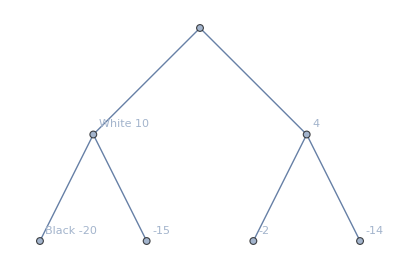

```mathematica
TreePlot[{1->2,3->1,2->4,2->5,3->6,3->7},VertexLabels->{2->Row[{"White ",10}],3->4,4->Row[{"Black ",-20}],5->-15,6->-2,7->-14},ImageSize->400]
```

The tree looks like this.

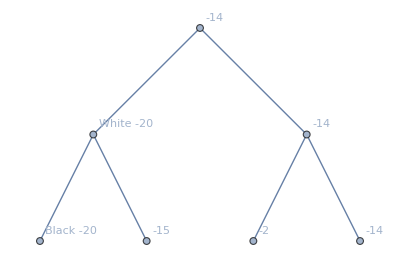

```mathematica
TreePlot[{1->2,3->1,2->4,2->5,3->6,3->7},VertexLabels->{1->-14,2->Row[{"White ",-20}],3->-14,4->Row[{"Black ",-20}],5->-15,6->-2,7->-14},ImageSize->400]
```

#### Depth 3

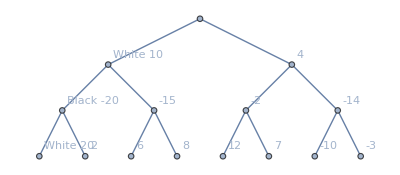

```mathematica
TreePlot[{1->2,3->1,2->4,2->5,3->6,3->7,4->8,4->9,5->10,5->11,6->12,6->13,7->14,7->15},VertexLabels->{2->Row[{"White ",10}],3->4,4->Row[{"Black ",-20}],5->-15,6->-2,7->-14,8->Row[{"White ",20}],9->2,10->6,11->8,12->12,13->7,14->-10,15->-3},ImageSize->400]
```

Leftmost, white would choose the move that gives 20 if black chose the move that gave -20. Next white would choose the move that would give 8 if black chose the move that gave -15, so black would choose the move that gives -15. Next white would choose the move giving 12 if black chose the move that gave -2. White would choose the move that gives -3 if black chose the move that gives -14. So black would choose the move giving -14. So white would choose the move that would score 8.

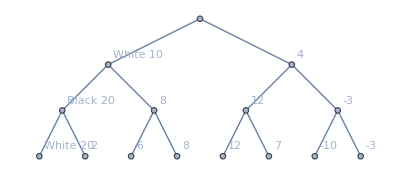

```mathematica
TreePlot[{1->2,3->1,2->4,2->5,3->6,3->7,4->8,4->9,5->10,5->11,6->12,6->13,7->14,7->15},VertexLabels->{2->Row[{"White ",10}],3->4,4->Row[{"Black ",20}],5->8,6->12,7->-3,8->Row[{"White ",20}],9->2,10->6,11->8,12->12,13->7,14->-10,15->-3},ImageSize->400]
```

Black would choose the move giving 8 on the left side of the tree and on the right black would choose the move giving -3. So white would choose the move giving 8.

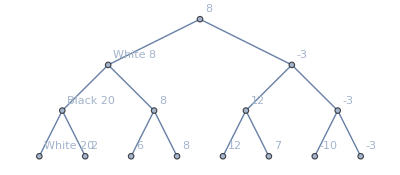

```mathematica
TreePlot[{1->2,3->1,2->4,2->5,3->6,3->7,4->8,4->9,5->10,5->11,6->12,6->13,7->14,7->15},VertexLabels->{1->8,2->Row[{"White ",8}],3->-3,4->Row[{"Black ",20}],5->8,6->12,7->-3,8->Row[{"White ",20}],9->2,10->6,11->8,12->12,13->7,14->-10,15->-3},ImageSize->400]
```

### Alpha Beta Pruning

As in minimax, Black gets a 6 in the lower left. Moving to the right from black with the 6 and going down on the left. White gets a 7 at least so no point in examining the score to its right. Black chooses the move that give it 6, so White gets a 6 for that branch. Moving to the right, White will choose the move that gives a 2 so black’s score is 2. Black wants to minimize, so moving to the right could only be less than or equal to 2 and White’s other move gives it a 6, so the rest of this branch does not need to be considered and White has a 6 for this position.

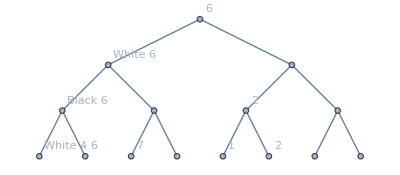

```mathematica
TreePlot[{1->2,3->1,2->4,2->5,3->6,3->7,4->8,4->9,5->10,5->11,6->12,6->13,7->14,7->15},VertexLabels->{1->6,2->Row[{"White ",6}],4->Row[{"Black ",6}],6->2,8->Row[{"White ",4}],9->6,10->7,12->1,13->2},ImageSize->400]
```

## AlphaBeta Function Video 59

static int AlphaBeta(int alpha, int beta, int depth, S_BOARD *pos, S_SEARCHINFO *info, int DoNull) {

	if(depth == 0) {
		info->nodes++;
		return EvalPosition(pos);
	}
	
	// A node has been visited so increment nodes.
	info->nodes++;
	
	if(IsRepetition(pos) || pos->fiftyMove >= 100) {
		//position is a draw
		return 0;
	}
	
	if(pos->ply > MAXDEPTH - 1) {
		//depth is the maximum allowed, principal variation array only holds MAXDEPTH moves
		return EvalPosition(pos);
	}
	
	S_MOVELIST list[1];
          GenerateAllMoves(pos,list);
      
          int MoveNum = 0;
	int Legal = 0; // once gone through all the moves, if none legal, the position is either checkmate or stalemate
	int OldAlpha = alpha;// once gone through the moves, if alpha no longer equal to OldAlpha, store the best move found in the principal variation
	// a move has been found which beat alpha
	int BestMove = NOMOVE;
	int Score = -INFINITE;
	
	//very similar to perft
	for(MoveNum = 0; MoveNum < list->count; ++MoveNum) {	
       
                   if ( !MakeMove(pos,list->moves[MoveNum].move))  {
                        continue;
                    }
        
                    Legal++;
                    //use negamax
                    Score = -AlphaBeta( -beta, -alpha, depth-1, pos, info, TRUE);		
                    TakeMove(pos);
		
		if(Score > alpha) {
			//improve alpha
			if(Score >= beta) {
			          //have a beta cutoff
				return beta;
			}
			alpha = Score;
			BestMove = list->moves[MoveNum].move;
		}		
           }
	
	if(Legal == 0) {
		if(SqAttacked(pos->KingSq[pos->side],pos->side^1,pos)) {
		           //no legal moves and in check - it is checkmate
			//return distance to mate from the root
			return -MATE + pos->ply;
		} else {
			//stalemate
			return 0;
		}
	}
	
	if(alpha != OldAlpha) {
	           //alpha has been improved so store the best move for this position which will then end up in the pv array
		StorePvMove(pos, BestMove);
	}
	
	//if alpha was not improved, just return it
	return alpha;
}

## AlphaBeta Function

#define infinite 30000
#define ISMATE (infinite - MAXDEPTH)

int rootDepth;

static void CheckUp(S_SEARCHINFO* info) {
    // .. check if time up, or interrupt from GUI
    if (info->timeset == TRUE && GetTimeMs() > info->stoptime) {
        info->stopped = TRUE;
    }

    ReadInput(info);
}

static int AlphaBeta(int alpha, int beta, int depth, S_BOARD* pos, S_SEARCHINFO* info) {

    if (depth == 0) {
        return Quiescence(alpha, beta, pos, info);
    }

    if ((info->nodes & 2047) == 0) {
        CheckUp(info);
    }

    info->nodes++;

    if ((IsRepetition(pos) || pos->fiftyMove >= 100) && pos->ply) {
        return 0;
    }

    if (pos->ply > MAXDEPTH - 1) {
        return EvalPosition(pos);
    }

    int InCheck = SqAttacked(pos->KingSq[pos->side], pos->side ^ 1, pos);

    if (InCheck == TRUE) {
        depth++;
    }

    int Score = -infinite;

    S_MOVELIST list[1];
    GenerateAllMoves(pos, list);

    int MoveNum = 0;
    int Legal = 0;
    int OldAlpha = alpha;
    int BestMove = NOMOVE;
    int PvMove = ProbePvTable(pos);
    Score = -infinite;

    if (PvMove != NOMOVE) {
        for (MoveNum = 0; MoveNum < list->count; ++MoveNum) {
            if (list->moves[MoveNum].move == PvMove) {
                list->moves[MoveNum].score = 2000000;
                break;
            }
        }
    }

    for (MoveNum = 0; MoveNum < list->count; ++MoveNum) {

        PickNextMove(MoveNum, list);

        //if move is illegal, go to next one
        if (!MakeMove(pos, list->moves[MoveNum].move)) {
            continue;
        }

        //if move is legal
        Legal++;
        Score = -AlphaBeta(-beta, -alpha, depth - 1, pos, info);
        TakeMove(pos);

        if (info->stopped == TRUE) {
            return 0;
        }

        if (Score > alpha) {
            if (Score >= beta) {
                if (Legal == 1) {
                    info->fhf++;
                }
                info->fh++;

                if (!(list->moves[MoveNum].move & MFLAGCAP)) {
                    pos->searchKillers[1][pos->ply] = pos->searchKillers[0][pos->ply];
                    pos->searchKillers[0][pos->ply] = list->moves[MoveNum].move;
                }

                return beta;
            }
            alpha = Score;
            BestMove = list->moves[MoveNum].move;
            if (!(list->moves[MoveNum].move & MFLAGCAP)) {
                pos->searchHistory[pos->pieces[FROMSQ(BestMove)]][TOSQ(BestMove)] += depth;
            }
        }
    }

    if (Legal == 0) {
        if (InCheck) {
            return -infinite + pos->ply;
        }
        else {
            return 0;
        }
    }

    if (alpha != OldAlpha) {
        StorePvMove(pos, BestMove);
    }

    return alpha;
}

## Move Ordering - Killer, History Heuristics, PV Move

## Quiescence - Getting rid of the horizon effect

static int Quiescence(int alpha, int beta, S_BOARD* pos, S_SEARCHINFO* info) {

    if ((info->nodes & 2047) == 0) {
        CheckUp(info);
    }

    info->nodes++;

    if (IsRepetition(pos) || pos->fiftyMove >= 100) {
        return 0;
    }

    if (pos->ply > MAXDEPTH - 1) {
        return EvalPosition(pos);
    }

    int Score = EvalPosition(pos);

    if (Score >= beta) {
        return beta;
    }

    if (Score > alpha) {
        alpha = Score;
    }

    S_MOVELIST list[1];
    GenerateAllCaps(pos, list);

    int MoveNum = 0;
    int Legal = 0;
    int OldAlpha = alpha;
    int BestMove = NOMOVE;
    Score = -infinite;
    int PvMove = ProbePvTable(pos);

    if (PvMove != NOMOVE) {
        for (MoveNum = 0; MoveNum < list->count; ++MoveNum) {
            if (list->moves[MoveNum].move == PvMove) {
                list->moves[MoveNum].score = 2000000;
                break;
            }
        }
    }

    for (MoveNum = 0; MoveNum < list->count; ++MoveNum) {

        PickNextMove(MoveNum, list);

        if (!MakeMove(pos, list->moves[MoveNum].move)) {
            continue;
        }

        Legal++;
        Score = -Quiescence(-beta, -alpha, pos, info);
        TakeMove(pos);

        if (info->stopped == TRUE) {
            return 0;
        }

        if (Score > alpha) {
            if (Score >= beta) {
                if (Legal == 1) {
                    info->fhf++;
                }
                info->fh++;
                return beta;
            }
            alpha = Score;
            BestMove = list->moves[MoveNum].move;
        }
    }

    if (alpha != OldAlpha) {
        StorePvMove(pos, BestMove);
    }

    return alpha;
}

## UCI Protocol

Detailed here

https://www.stmintz.com/ccc/index.php?id=141612

## UCI Implementation in the Engine

#define INPUTBUFFER 400 * 6

// go depth 6 wtime 180000 btime 100000 binc 1000 winc 1000 movetime 1000 movestogo 40
void ParseGo(char* line, S_SEARCHINFO* info, S_BOARD* pos) {

    int depth = -1, movestogo = 30, movetime = -1;
    int time = -1, inc = 0;
    char* ptr = NULL;
    info->timeset = FALSE;

    if ((ptr = strstr(line, “infinite”))) {
        ;
    }

    if ((ptr = strstr(line, “binc”)) && pos->side == BLACK) {
        inc = atoi(ptr + 5);
    }

    if ((ptr = strstr(line, “winc”)) && pos->side == WHITE) {
        inc = atoi(ptr + 5);
    }

    if ((ptr = strstr(line, “wtime”)) && pos->side == WHITE) {
        time = atoi(ptr + 6);
    }

    if ((ptr = strstr(line, “btime”)) && pos->side == BLACK) {
        time = atoi(ptr + 6);
    }

    if ((ptr = strstr(line, “movestogo”))) {
        movestogo = atoi(ptr + 10);
    }

    if ((ptr = strstr(line, “movetime”))) {
        movetime = atoi(ptr + 9);
    }

    if ((ptr = strstr(line, “depth”))) {
        depth = atoi(ptr + 6);
    }

    if (movetime != -1) {
        time = movetime;
        movestogo = 1;
    }

    info->starttime = GetTimeMs();
    info->depth = depth;

    if (time != -1) {
        info->timeset = TRUE;
        time /= movestogo;
        time -= 50;
        info->stoptime = info->starttime + time + inc;
    }

    if (depth == -1) {
        info->depth = MAXDEPTH;
    }

    printf(“time:%d start:%d stop:%d depth:%d timeset:%d\n”,
        time, info->starttime, info->stoptime, info->depth, info->timeset);
    SearchPosition(pos, info);
}

void ParsePosition(char* lineIn, S_BOARD* pos) {

    lineIn += 9;
    char* ptrChar = lineIn;

    if (strncmp(lineIn, “startpos”, 8) == 0) {
        ParseFen(START_FEN, pos);
    }
    else {
        ptrChar = strstr(lineIn, “fen”);
        if (ptrChar == NULL) {
            ParseFen(START_FEN, pos);
        }
        else {
            ptrChar += 4;
            ParseFen(ptrChar, pos);
        }
    }

    ptrChar = strstr(lineIn, “moves”);
    int move;

    if (ptrChar != NULL) {
        ptrChar += 6;
        while (*ptrChar) {
            move = ParseMove(ptrChar, pos);
            if (move == NOMOVE) break;
            MakeMove(pos, move);
            pos->ply = 0;
            while (*ptrChar && *ptrChar != ‘ ‘) ptrChar++;
            ptrChar++;
        }
    }
    PrintBoard(pos);
}

void Uci_Loop(S_BOARD* pos, S_SEARCHINFO* info) {

    setbuf(stdin, NULL);
    setbuf(stdout, NULL);

    char line[INPUTBUFFER];
    printf(“id name %s\n”, NAME);
    printf(“id author Jay Warendorff\n”);
    printf(“uciok\n”);

    while (TRUE) {
        memset(&line[0], 0, sizeof(line));
        fflush(stdout);
        if (!fgets(line, INPUTBUFFER, stdin))
            continue;

        if (line[0] == ‘\n’)
            continue;

        if (!strncmp(line, “isready”, 7)) {
            printf(“readyok\n”);
            continue;
        }
        else if (!strncmp(line, “position”, 8)) {
            ParsePosition(line, pos);
        }
        else if (!strncmp(line, “ucinewgame”, 10)) {
            ParsePosition(“position startpos\n”, pos);
        }
        else if (!strncmp(line, “go”, 2)) {
            ParseGo(line, info, pos);
        }
        else if (!strncmp(line, “quit”, 4)) {
            info->quit = TRUE;
            break;
        }
        else if (!strncmp(line, “uci”, 3)) {
            printf(“id name %s\n”, NAME);
            printf(“id author Jay Warendorff\n”);
            printf(“uciok\n”);
        }
        if (info->quit) break;
    }
}

## Connect GUI

int InputWaiting()
{
    static int init = 0, pipe;
    static HANDLE inh;
    DWORD dw;

    if (!init) {
        init = 1;
        inh = GetStdHandle(STD_INPUT_HANDLE);
        pipe = !GetConsoleMode(inh, &dw);
        if (!pipe) {
            SetConsoleMode(inh, dw & ~(ENABLE_MOUSE_INPUT | ENABLE_WINDOW_INPUT));
            FlushConsoleInputBuffer(inh);
        }
    }
    if (pipe) {
        if (!PeekNamedPipe(inh, NULL, 0, NULL, &dw, NULL)) return 1;
        return dw;
    }
    else {
        GetNumberOfConsoleInputEvents(inh, &dw);
        return dw <= 1 ? 0 : dw;
    }
}

void ReadInput(S_SEARCHINFO* info) {
    int             bytes;
    char            input[256] = “”, * endc;

    if (InputWaiting()) {
        info->stopped = TRUE;
        do {
            bytes = read(fileno(stdin), input, 256);
        } while (bytes < 0);
        endc = strchr(input, ‘\n’);
        if (endc) *endc = 0;

        if (strlen(input) > 0) {
            if (!strncmp(input, “quit”, 4)) {
                info->quit = TRUE;
            }
        }
        return;
    }
}

## Main

int main() {

    // debug mode variable
    int debug = 0;

    // if debugging - debug 1
    if (debug)
    {
        AllInit();

        S_BOARD pos[1];
        S_SEARCHINFO info[1];
        info->quit = FALSE;
        pos->PvTable->pTable = NULL;
        InitPvTable(pos->PvTable);

        //Perft results depth 3 - 8902, depth 4 - 197,281, depth 5 - 4,865,609, depth 6 - 119,060,324

        ParseFen(START_FEN, pos);
        PerftTest(6, pos);
        while (1);
    }
    else
    {
        AllInit();

        S_BOARD pos[1];
        S_SEARCHINFO info[1];
        info->quit = FALSE;
        pos->PvTable->pTable = NULL;
        InitPvTable(pos->PvTable);
        setbuf(stdin, NULL);
        setbuf(stdout, NULL);

        char line[256];
        while (TRUE) {
            memset(&line[0], 0, sizeof(line));

            fflush(stdout);
            if (!fgets(line, 256, stdin))
                continue;
            if (line[0] == ‘\n’)
                continue;
            if (!strncmp(line, “uci”, 3)) {
                Uci_Loop(pos, info);
                if (info->quit == TRUE) break;
                continue;
            }
            else if (!strncmp(line, “quit”, 4)) {
                break;
            }
        }

        free(pos->PvTable->pTable);
    }
    return 0;
}

## Further Development

### Pseudo-legal Move Generator

Use a pseudo-legal move generator instead of a legal one. Once you implement a decent move ordering in your engine, the first several moves it looks at will hopefully be the best, and so it won’t waste time looking at all the other moves, and won’t spend the extra work of calculating if they’re legal. But with a fully legal move generator, the time is spent verifying every move is legal regardless of if you actually have to.

### Board Representation Using Bitboards

Easier to improve the evaluation function.

### Staged Move Generation, Null Move Pruning, Transposition Table, Razoring, Futility Pruning, Late Move Reductions, Aspiration Window

https://www.chessprogramming.org/Tapered_Eval

From http://web.archive.org/web/20070826142534/http://www.seanet.com/~brucemo/topics/aspiration.htm

An aspiration window is an enhancement to iterative deepening.  The simplest implementation of iterative deepening works as follows:

for (depth = 1;; depth++) {
val = AlphaBeta(depth, -INFINITY, INFINITY);
 if (TimedOut())
break;
}

Alpha-beta is called with a “window” of +/- INFINITY, presumably large positive and negative values.

It is possible to enhance this to a degree by making the assumption that the value of the search in the next iteration is not likely to be too much different from the value of the search in the iteration just completed.  Here’s the code:

#define valWINDOW  50

alpha = -INFINITY;
beta = INFINITY;
for (depth = 1;;) {
val = AlphaBeta(depth, alpha, beta);
if (TimedOut())
break;
if ((val <= alpha) || (val >= beta)) {
alpha = -INFINITY;    // We fell outside the window, so try again with a
beta = INFINITY;      //  full-width window (and the same depth).
continue;
}
alpha = val - valWINDOW;  // Set up the window for the next iteration.
beta = val + valWINDOW;
depth++;
}

### Pawn Hash Table

#### Alvin Peng 5/22/22 on Talk Chess - What pruning techniques should I add to my engine?

Instead of reevaluating pawn structure every time you call your evaluation function, you can evaluate it once and save that evaluation in a dedicated hash table. Pawn structure isn’t very dynamic, so pawn tables have very high hit rates. You index the pawn hash table with a pawn key, which is like the zobrist hash key but only for pawns.

Material hash tables store information regarding piece counts. You could use it to store things like game phase or material imbalance. Lots of chess engines keep an incrementally updated material key, which updates whenever there is a capture or promotion. This key is used to index the material hash table, as well as check for drawn material.

In terms of resources, you could take a look at implementations in other chess engines. Many of them will have a “pawnKey” or “materialKey” member in their board structures.

#### H. G. Muller 5/22/22 on Talk Chess - What pruning techniques should I add to my engine?

The idea behind these hash tables is similar to that of the Transposition Table: you map the features for which you want to tabulate something onto a number through Zobrist hashing to get a hash key. For the TT you want the key to be dependent on all pieces and their location, plus a number of other infos (side to move, castling and e.p. rights). So you give every (color, pieceType, square) combination a different random number as base key, and XOR all of those. Since in general only one of the pieces moves, this is easy to update incrementally.

The Pawn key should only identify the Pawn structure, so you only need to have a key for every Pawn (and possibly the e.p. rights). You could calculate it exactly the same as the TT hash key, by setting the base keys for all non-Pawns to 0. For the material key you are only interested in what pieces are on the board, not where these are. So you only need a base key for every (color, pieceType) combination. You would only have to update it for moves that change material, i.e. for the captured piece, and for promotions.

The hashing scheme is always the same: part of the key you use to derive an ‘index’ to a table, which tells where in the table the information for this position / pawn structure / material combination is stored. In that place you store the remaining part of the key as ‘signature’, so you can test if the other data that is stored there indeed corresponds to the case you were looking for. If that signature matches your key, you use the information. If it doesn’t, you have to calculate the information you were hoping to find from scratch for the current position, and you store it in the table (together with the signature for the current position). And then use it.

The idea is that most of the time (say 95% or 99% of the cases) you would have a matching signature, and can use the information without calculating anything. Then you would only have to do an actual calculation in 5% or 1% of the cases, effectively speeding up the calculation by a factor 20 or 100. Then you don’t care too much whether the calculation was time-consuming.

The tables could store all kinds of data in addition to the signature. E.g. for a Pawn table you could have the total score (e.g. white POV) for all passers, doubled Pawns, isolated Pawns etc. You could also store information that helps speeding up other evaluation terms that do not purely depend on Pawns. E.g. you could store the number of Pawns of either color on light and dark squares, to know whether you have a good or a bad Bishop. Or you could list half-open files for white and black (e.g. as a byte where each bit represents a file), to give a bonus for Rooks being on these files. You could store the location and promotion square of the most advanced passer, to quickly calculate in a Pawn ending whether a player has an unstoppable passer. You could calculate the quality of the King-side and Queen-side Pawn shield that a King would have when it had castled in that direction, for use if the King is indeed on the c- or g-file, or determining the value of castling rights if it can still castle.

In the material table you could store score corrections on the PST + material score for combinations of pieces. Such as the Bishop pair. Or factors with which the normal evaluation score should be multiplied for white and black (whichever naively seems to be ahead), to indicate drawishness. (E.g. for KBK you would want to multiply with 0, so that the naive +3 score is annihilated, and for KBPKN you would like a multiplier close to zero, to express that the Pawn will likely be lost through a Knight sacrifice.) Or you could indicate that a special evaluation routine should be called, and which one. (E.g. for KPK, which would determine whether it is a win and a draw depending on the actual K and P locations.)

## Fix for Null Move Pruning

If you followed VICE exactly you’ll have the condition that the side to move has to have a “big piece” aka non-pawn, non-king to perform a null move, however VICE mistakenly counts the king as a big piece meaning it will always allow null moves. Fixing this, not counting the king, in my engine (also based on VICE) allowed it to solve a lot of zugzwang positions it previously could not.

## References

http://www.brucemo.com/compchess/programming/index.htm

https://rustic-chess.org/

The classical approach to generating bitboard sliding piece attacks:

https://www.chessprogramming.org/Classical_Approach

https://www.chessprogramming.org/Aspiration_Windows